```mathematica
success=ReadList["C:\\Users\\Christopher Plumberg\\Downloads\\success_sph_lowTol.dat",Real];
fail=ReadList["C:\\Users\\Christopher Plumberg\\Downloads\\error_sph_lowTol.dat",Real];
success=ArrayReshape[success,{Length[success]/6,6}];
fail=ArrayReshape[fail,{Length[fail]/6,6}];
```

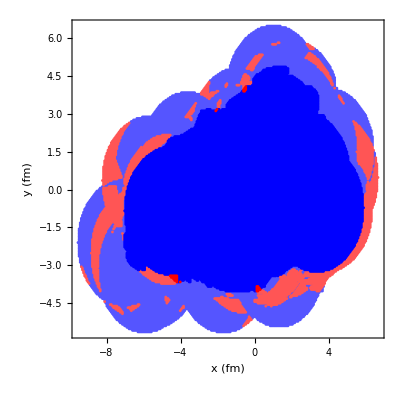

```mathematica
eFO=0.266112;
ListPlot[{(Select[success,#[[3]]<eFO&])[[;;,{1,2}]],(Select[fail,#[[3]]<eFO&])[[;;,{1,2}]],(Select[success,#[[3]]≥eFO&])[[;;,{1,2}]],(Select[fail,#[[3]]≥eFO&])[[;;,{1,2}]]},PlotStyle->{{PointSize[0.005],Blue//Lighter},{PointSize[0.005],Red//Lighter},{PointSize[0.005],Blue},{PointSize[0.005],Red}},AspectRatio->1,Frame->True,FrameLabel->{"x (fm)","y (fm)"}]
(*Export[NotebookDirectory[]<>"ICCING_and_SPH.pdf",%]*)
```

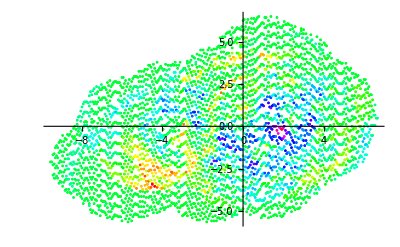

```mathematica
ListPlot[{#}&/@(success~Join~fail)[[;;;;10,{1,2}]],PlotStyle->Evaluate[Hue/@(((success~Join~fail)[[;;;;10,4]]-Min[(success~Join~fail)[[;;;;10,4]]])/(Max[(success~Join~fail)[[;;;;10,4]]]-Min[(success~Join~fail)[[;;;;10,4]]]))]]
(*Export[NotebookDirectory[]<>"eSPH.pdf",%]*)
```

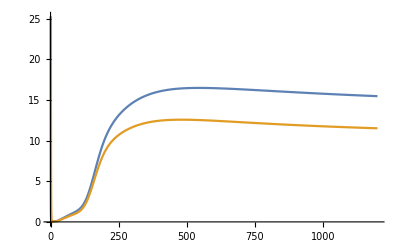

50.2335

10587.1

```mathematica
tmp=ReadList["C:\\Users\\Christopher Plumberg\\Downloads\\eos_mu0.dat",Real];
tmp=ArrayReshape[tmp,{Length[tmp]/11,11}][[;;,{1,6,10}]];
tmp[[;;,2]]*=tmp[[;;,1]]^3/197.33^3;
tmp[[;;,3]]*=tmp[[;;,1]]^4/197.33^3;
s=Interpolation[tmp[[;;,{1,2}]]];
e=Interpolation[tmp[[;;,{1,3}]]];
Plot[{s[T]*197.33^3/T^3,e[T]*197.33^3/T^4},{T,0,1200}]
s[298]
e[290]
```